Create a CAMB input file for the Planck13 LCDM cosmology:

```mathematica
Needs["DeepZot`CosmoTools`"]
```

```mathematica
createCosmology[Planck13]
```

```mathematica
SetDirectory["/Users/david/Cosmo/DESC/DarkEnergySchool/LargeScaleStructureStatistics/camb/"]
```

/Users/david/Cosmo/DESC/DarkEnergySchool/LargeScaleStructureStatistics/camb

```mathematica
exportToCamb["Planck13.camb",Planck13,redshifts->{0,1.2},kmax->100]
```

Planck13.camb

```mathematica
Needs["DeepZot`PowerTools`"]
```

```mathematica
Planck13Data=ReadList["Planck13_matterpower_1.dat",Number,RecordLists->True];
```

```mathematica
Planck13Pk=makePower[Planck13Data];
```

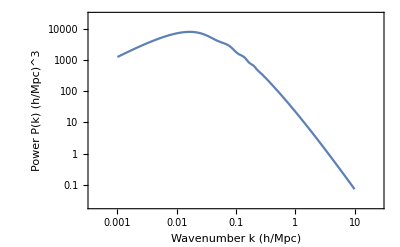

```mathematica
LogLogPlot[Planck13Pk[k],{k,0.001,10},GridLines->Automatic,Frame->True,FrameLabel->{"Wavenumber k (h/Mpc)","Power P(k) (h/Mpc)^3"}]
```

Compare the corresponding correlation functions:

```mathematica
{rmin,rmax,veps}={1,200,0.001};
Planck13Xi=sbTransform[Planck13Pk,rmin,rmax,0,veps];
```

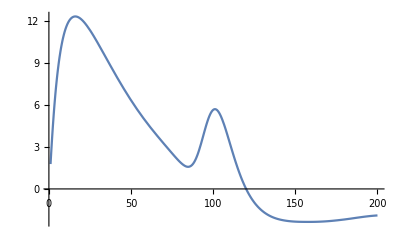

```mathematica
Plot[r^2Planck13Xi[r],{r,rmin,rmax}]
```

```mathematica
cLight=Convert[SpeedOfLight,Kilo Meter/Second]/(Kilo Meter/Second)
```

149896229/500

```mathematica
Sqrt[2Ωmat[Planck13][0](H0[Planck13]/cLight)^2 3403]
```

0.0104082

```mathematica
Integrate[Sinc[k r],{k,0,Infinity},Assumptions->{r>0}]/(2π^2)
```

1/(4 π r)